#### Setup of the objective function

```mathematica
(*Input constants, along with the above examples*)
ΔρAB=(ρA-ρB);ΔρAC=(ρA-ρC);ΔρBC=(ρB-ρC);

objfun[LAB_?NumberQ,LAC_?NumberQ,LBC_?NumberQ,ΔPAB_?NumberQ,ΔPAC_?NumberQ,ΔPBC_?NumberQ ,R_?NumberQ]:=(
(*eqn 1 and 2 are the paired differential equations to be solved*)
eqn1[r_Symbol,z_Symbol,j_,L_,σ_,ΔP_,Δρ_] =
r''[j]==z'[j](L/σ ΔP -L/σ Δρ g z[j]+z'[j]/r[j]);
eqn2[r_Symbol,z_Symbol,j_,L_,σ_,ΔP_,Δρ_]= 
z''[j]==-r'[j](L/σ ΔP -L/σ Δρ g z[j]+z'[j]/r[j]);

(*each eqn must be solved for each boundry between the fluids, leading to 6 total eqns*)
eqns =
{eqn1[rAB,zAB,j,LAB,σAB,ΔPAB,ΔρAB],
eqn2[rAB,zAB,j,LAB,σAB,ΔPAB,ΔρAB],
eqn1[rAC,zAC,j,LAC,σAC,ΔPAC,ΔρAC],
eqn2[rAC,zAC,j,LAC,σAC,ΔPAC,ΔρAC],
eqn1[rBC,zBC,j,LBC,σBC,ΔPBC,ΔρBC],
eqn2[rBC,zBC,j,LBC,σBC,ΔPBC,ΔρBC]};

(* NDSolve with an input of t=0 encounters a singularity, so we do one Euler step and then turned the solving back over to NDSolve*)
step = .0001;
icsfs = {(*resulting ics after one euler step*)
zAB[step]==0,zAB'[step]==step*(-LAB^2/(2 σAB ) ΔPAB),rAB[step]== step*LAB,rAB'[step]==LAB,
zAC[step]==0,zAC'[step]==step*(-LAC^2/(2 σAC ) ΔPAC),rAC[step]==step*LAC,rAC'[step]==LAC,
zBC[step]==τ*step,zBC'[step]==τ+Sqrt[LBC^2-τ^2](LBC ΔPBC/σBC+τ/Σ)step,rBC[step]==Σ-Sqrt[LBC^2-τ^2]step,rBC'[step]==-Sqrt[LBC^2-τ^2]+τ(LBC ΔPBC/σBC+τ/Σ)step};

(*command to actually run the solution*)
sol =NDSolve[{eqns,icsfs},{rAB,zAB,rAC,zAC,rBC,zBC},{j,step,1}];

(*the final values of each eqn in important for the boundary conditions, so we find them here*)
ABfinal = (zAB/.Flatten[sol])[1];
ACfinal= (zAC/.Flatten[sol])[1];
BCfinal= (zBC/.Flatten[sol])[1];



(* These shifts translate the curves vertically.  The AB, AC interfaces are shifted to match the BC interface.*)
ABshift = ABfinal;
ACshift = ACfinal;
BCshift = BCfinal;
rABf[j_] =(rAB/.Flatten[sol])[j];
zABf[j_] =(zAB/.Flatten[sol])[j]-ABshift;
rACf[j_] =(rAC/.Flatten[sol])[j];
zACf[j_] =(zAC/.Flatten[sol])[j]-ACshift;
rBCf[j_] =(rBC/.Flatten[sol])[j];
zBCf[j_] =(zBC/.Flatten[sol])[j]-BCshift;

(* Compute AC volume. This volume will be positive/negative if the AC interface lies above/below the z=0 level.  We assume the interface does not cross z=0, but attains z=0 at j=1 where the interfaces meet. *)
vAC=-NIntegrate[Pi zACf'[j] (rACf[j])^2,{j,0,1},PrecisionGoal->4];

(* Compute AB volume. Assuming the interface lies below the z=0 level, this volume will be positive*)
vAB=NIntegrate[Pi zABf'[j] (rABf[j])^2,{j,0,1},PrecisionGoal->4];

(* A simple test to see if lens is upside down. *)
If[ACshift<ABshift,testtext = "Right side up!",testtext = "Upside down!"];

(*the shifts change the equation for ΔP(pressure)*)
ΔPABnew = ΔPAB + ΔρAB g ABshift;
ΔPACnew = ΔPAC + ΔρAC g ACshift;
ΔPBCnew = ΔPBC + ΔρBC g BCshift;

(*these are the boundary conditions, they define how the three fluid boundaries come together*)
(* Force balance for the r component. *)
fbr=(σAB Normalize[{rABf'[1],zABf'[1]}]+σBC Normalize[{rBCf'[1],zBCf'[1]}]+σAC Normalize[{rACf'[1],zACf'[1]}])[[1]];

(* Force balance for the z component. *)
fbz=(σAB Normalize[{rABf'[1],zABf'[1]}]+σBC Normalize[{rBCf'[1],zBCf'[1]}]+σAC Normalize[{rACf'[1],zACf'[1]}])[[2]];

(* Pressure balance. *)
pb = -ΔPACnew+ΔPABnew+ΔPBCnew;

(* The objective function *)
{rABf[1]-R,rACf[1]-R,rBCf[1]-R,vAC+vAB-volume,fbr,fbz,pb});
```

## The computation: abort when you have solutions

```mathematica
(* Here we estimate the parameters LAB,LAC,LBC,ΔPAB,ΔPAC,ΔPBC,R, via rootfinding to satisfy boundary conditions.  Random guesses are used to initialize the root finding.*)
Clear["Global`*"]
ρA =1.14;  (* resin density g/mL] *)
ρB=1; (* water density [g/mL] *)
ρC=0; (* air density [g/mL] *)
Σ = 2; (* 0.952*)(* radius of the container [cm]*)
g = 980.665;  (* Acceleration due to gravity. [cm/s^2]*)
τ = 0;
σAC;(* 36; *) (* resin to air surface tension [dynes/cm] *)
σAB ;
σBC; (* new water to air surface tension [dynes/cm], old was 72.8 *)
k = 1;
volume = 0.2;
genfun[AB_, AC_, BC_]:=(
σAB=AB;(* 9; *) (* resin to water surface tension [dynes/cm] *)
σAC=AC;
σBC = BC;
sols={};
Clear[LAB,LAC,LBC,ΔPAB,ΔPAC,ΔPBC,R];
SetSharedVariable[sols];
Llowlim = .4;
Luplim = .8;
ΔPlowlim = -50;
ΔPuplim = 48;
(*variable to check whether any of the functions has found a correct solution, this must be false for another attempt to be made*)
foundgood = False;
(*set this as a shared variable accross all the parallel running functions*)
SetSharedVariable[foundgood];
ParallelDo[
(*if any of the cores has found a correct lens, do not try to produce one*)
If[foundgood== True, Abort[]];
Clear[LAB,LAC,LBC,ΔPAB,ΔPAC,ΔPBC,R];
(* find the zeroes for the objective function, this is parallely done across all avaialable cores*)
roots = FindRoot[objfun[LAB,LAC,LBC,ΔPAB,ΔPAC,ΔPBC,R],{LAB,RandomReal[{0.05,0.5}]},{LAC,RandomReal[{0.05,0.5}]},{LBC,-RandomReal[{0.05,0.5}]},{ΔPAB,RandomReal[{-50,50}]},{ΔPAC,RandomReal[{-50,50}]},{ΔPBC,RandomReal[{-50,50}]},{R,RandomReal[{0.05,0.5}]}, MaxIterations->30]//Quiet;
Set@@@roots;
Print["Attempt ",k,". Success? ",Norm[objfun[LAB,LAC,LBC,ΔPAB,ΔPAC,ΔPBC,R]]];
heightwidthratio = (zACf[0]-zABf[0])/(2rABf[1]);
acvolume = Abs[-Pi NIntegrate[ zACf'[j] (rACf[j])^2,{j,0,1}]];
(*These are the two checks to ensure that produced lenses are correct lenses. They check that the lens has a reasonable height to width ratio, and that the ac volume, that being the air resin interface, doesn't take up too large of a portion of the lens, I have good luck with the values put in here, though honestly they are just magic numbers and a more
scientific analysis could be done. *)
Print[ToString[heightwidthratio ]<>" ratio"];
Print[ToString[acvolume] <> " acvolume"];

If[Norm[objfun[LAB,LAC,LBC,ΔPAB,ΔPAC,ΔPBC,R]]<0.1 && 0<heightwidthratio<2 ,
Clear[LAB,LAC,LBC,ΔPAB,ΔPAC,ΔPBC,R];
AppendTo[sols,roots];
foundgood = True;];
Print[foundgood];
Clear[LAB,LAC,LBC,ΔPAB,ΔPAC,ΔPBC,R];
,{k,1,100}, Method->"FinestGrained"];
list=DeleteDuplicates[sols,Norm[({LAB,LAC,LBC,ΔPAB,ΔPAC,ΔPBC,R}/.#1)-({LAB,LAC,LBC,ΔPAB,ΔPAC,ΔPBC,R}/.#2)]<10^(-5)&]
);
```

## Visualization

InterpolatingFunction::dmval: Input value {0} lies outside the range of data in the interpolating function. Extrapolation will be used.

Attempt 3. Success? 2.69826×10^-13

InterpolatingFunction::dmval: Input value {0} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

0.320811 ratio

0.0789381 acvolume

True

InterpolatingFunction::dmval: Input value {0} lies outside the range of data in the interpolating function. Extrapolation will be used.

Attempt 1. Success? 36.4107

InterpolatingFunction::dmval: Input value {0} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-3.00413 ratio

0.00055904 acvolume

True

InterpolatingFunction::dmval: Input value {0} lies outside the range of data in the interpolating function. Extrapolation will be used.

Attempt 5. Success? 2.14048×10^-6

InterpolatingFunction::dmval: Input value {0} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

0.320811 ratio

0.078938 acvolume

True

InterpolatingFunction::dmval: Input value {0} lies outside the range of data in the interpolating function. Extrapolation will be used.

Attempt 2. Success? 25.5931

InterpolatingFunction::dmval: Input value {0} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-0.0864072 ratio

0.00921042 acvolume

True

InterpolatingFunction::dmval: Input value {0} lies outside the range of data in the interpolating function. Extrapolation will be used.

Attempt 4. Success? 26.4995

InterpolatingFunction::dmval: Input value {0} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

0.358625 ratio

0.00039704 acvolume

True

InterpolatingFunction::dmval: Input value {0} lies outside the range of data in the interpolating function. Extrapolation will be used.

Attempt 7. Success? 45.286

InterpolatingFunction::dmval: Input value {0} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

1.50695 ratio

0.0198945 acvolume

True

InterpolatingFunction::dmval: Input value {0} lies outside the range of data in the interpolating function. Extrapolation will be used.

Attempt 8. Success? 23.4482

InterpolatingFunction::dmval: Input value {0} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

0.597904 ratio

0.156345 acvolume

True

InterpolatingFunction::dmval: Input value {0} lies outside the range of data in the interpolating function. Extrapolation will be used.

Attempt 6. Success? 26.5199

InterpolatingFunction::dmval: Input value {0} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

0.894095 ratio

0.146437 acvolume

True

Info on plot below:

Test data: {LAB→0.62158,LAC→0.587152,LBC→-1.44453,ΔPAB→-148.832,ΔPAC→29.759,ΔPBC→0.380569,R→0.560262}

InterpolatingFunction::dmval: Input value {0} lies outside the range of data in the interpolating function. Extrapolation will be used.

Surface Tensions {σAB,σAC,σBC}[dyne/cm] = {62.97,35.91,72.8}

InterpolatingFunction::dmval: Input value {0.} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

Surface Tensions {σAB,σAC,σBC}[dyne/cm] = {62.97,35.91,72.8}

Density Differences {ΔρAB,ΔρAC,ΔρBC}[g/cm^3] = {0.14,1.14,1}

Force balance (in vector form): {-8.52651×10^-14,2.55795×10^-13}

Shifted values of {ΔPAB,ΔPAC,ΔPBC}[dynes/cm^2]: {-117.519,-117.138,0.38057}

Container radius [cm]: 2

Lens radius [cm]: 0.560262

Volume AB [cm^3]: 0.121062

Volume AC [cm^3]: 0.0789381

Volume [cm^3]:0.2

Height to Width Ratio: 0.320811

Right side up!

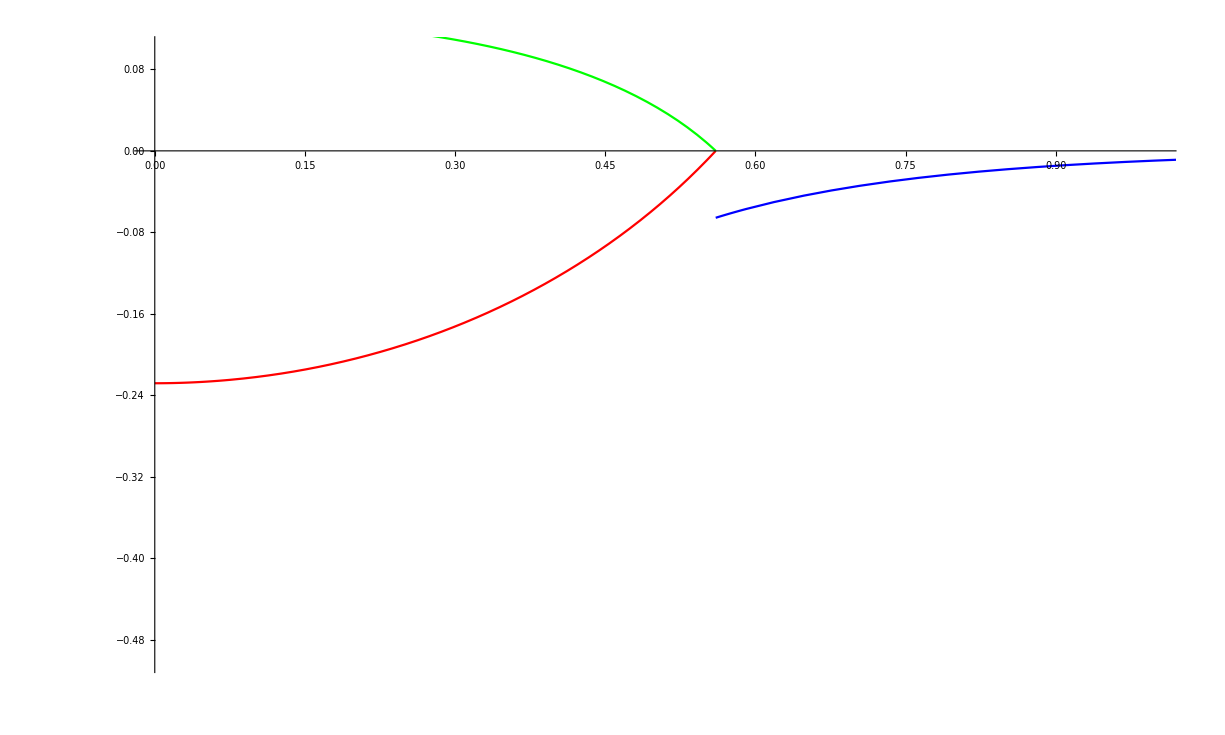

```mathematica
(*Here we print out useful data and graph the output*)
(*we run a for loop to produce the desired data, if you want to vary multiple variables, nest another for loop*)

(* To create multiple lenses, we can simply just run a for loop and iterate the values*)
(*setting up a list of different surface tension values for our mixtures, going by mass percent CN004*)

tensionlist = { {62.97, 35.91, 72.8}};
For[i = 1, i<=Length[tensionlist], i+=1,
ab = tensionlist[[i,1]];
ac = tensionlist[[i,2]];
bc =tensionlist[[i,3]];
Clear[LAB,LAC,LBC,ΔPAB,ΔPAC,ΔPBC,R];

(* pick which solution you want to visualize/get data for *)

list = genfun[ab, ac, bc];
roots = list[[k]];
Print["Info on plot below:"];
Print["Test data: ",roots];

Set@@@roots;
(* need to run to set values used below. *)
sol =objfun[LAB,LAC,LBC,ΔPAB,ΔPAC,ΔPBC,R];  
Print["Surface Tensions {σAB,σAC,σBC}[dyne/cm] = ", {σAB,σAC,σBC} ];
(* Export your lens shape data.  Ignore the warming :/ *)
If[foundgood == True,
Export[NotebookDirectory[]<>"ResultAB"<>ToString[k]<>"("<>ToString[ab]<>","<>ToString[ac]<>","<>ToString[σBC]<>")"<>".xls",Table[Flatten[{j,rABf[j],zABf[j]}],{j,0,1,.0001}],"XLS"];
Export[NotebookDirectory[]<>"ResultBC"<>ToString[k]<>"("<>ToString[ab]<>","<>ToString[ac]<>","<>ToString[σBC]<>")"<>".xls",Table[Flatten[{j,rBCf[j],zBCf[j]}],{j,0,1,.0001}],"XLS"];
Export[NotebookDirectory[]<>"ResultAC"<>ToString[k]<>"("<>ToString[ab]<>","<>ToString[ac]<>","<>ToString[σBC]<>")"<>".xls",Table[Flatten[{j,rACf[j],zACf[j]}],{j,0,1,.0001}],"XLS"];

Print["Surface Tensions {σAB,σAC,σBC}[dyne/cm] = ", {σAB,σAC,σBC} ];
Print["Density Differences {ΔρAB,ΔρAC,ΔρBC}[g/cm^3] = ",{ΔρAB,ΔρAC,ΔρBC}];
Print["Force balance (in vector form): ",{fbr,fbz}];
Print["Shifted values of {ΔPAB,ΔPAC,ΔPBC}[dynes/cm^2]: ",{ΔPABnew,ΔPACnew,ΔPBCnew}];
Print["Container radius [cm]: ",Σ];
Print["Lens radius [cm]: ",R];
Print["Volume AB [cm^3]: ",Pi NIntegrate[ zABf'[j] (rABf[j])^2,{j,0,1}]];
Print["Volume AC [cm^3]: ",-Pi NIntegrate[ zACf'[j] (rACf[j])^2,{j,0,1}]];
Print["Volume [cm^3]:",vAC+vAB];
Print["Height to Width Ratio: ",(zACf[0]-zABf[0])/(2rABf[1])//Quiet];(*untested*)
Print[testtext];
plot = ParametricPlot[Evaluate[
{{rABf[j],zABf[j]},
{rBCf[j],zBCf[j]},
{rACf[j],zACf[j]}}],
{j,step,1},AspectRatio->Automatic,PlotRange->{{0,1},{-.5,.1}},PlotStyle->{Red,Blue,Green}];
Print[plot]..
]];
```

```mathematica
.
```

```mathematica
.
```